```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
SetDirectory[basepath<>"/output"];
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
Needs["LatticeAnalysis`"];
 <<"LatticeAnalysis`"
(* do not keep track of intermediate results *)
$HistoryLength=0;
Needs["FourierSeries`"]
lata=0.11403
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

0.11403

#### Open Database

```mathematica
AmpDB = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_bL_bT_bevenodd.bidatex"]
AmpDBPbbsq = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_Pb32by2Pi_bsq_bevenodd.bidatex"]
```

< -MemDB- {A,bL,bNum,bT,data,EN,etav,MN,PL,zta}>

< -MemDB- {A,bNum,bsquare,data,EN,etav,MN,Pb32by2Pi,PL,zta}>

```mathematica
Mass = MemDBGet[AmpDB,MemDBSelect[AmpDB,{PL->-1}],{MN}]//Union
MassMeV=(Mass[[1,1]]/(lata))*197.32698
 MemDBGet[AmpDB,MemDBSelect[AmpDB,{PL->-1}],{zta}]//Union
```

{{⟨0.6228(28)⟩_(RowBox[{)}}

⟨1.0778(48) × 10⟩_(RowBox[{)

{{⟨0.09077(75)⟩_(RowBox[{)}}

```mathematica
bLbTlist=MemDBGet[AmpDB,MemDBSelect[AmpDB,{}],{bL,bT}]//Union;
bLbT0list=Append[#,0]&/@bLbTlist;
bLbT0list//Sort
Length[bLbT0list//Sort]
```

{{-8,-2,0},{-8,2,0},{-6,-3,0},{-6,3,0},{-5,-5,0},{-5,5,0},{-4,-4,0},{-4,-2,0},{-4,-1,0},{-4,1,0},{-4,2,0},{-4,4,0},{-3,-6,0},{-3,-3,0},{-3,3,0},{-3,6,0},{-2,-4,0},{-2,-2,0},{-2,-1,0},{-2,1,0},{-2,2,0},{-2,4,0},{-1,-2,0},{-1,-1,0},{-1,1,0},{-1,2,0},{0,-7,0},{0,-6,0},{0,-5,0},{0,-4,0},{0,-3,0},{0,-2,0},{0,-1,0},{0,0,0},{0,1,0},{0,2,0},{0,3,0},{0,4,0},{0,5,0},{0,6,0},{0,7,0},{1,-2,0},{1,-1,0},{1,1,0},{1,2,0},{2,-4,0},{2,-2,0},{2,-1,0},{2,1,0},{2,2,0},{2,4,0},{3,-6,0},{3,-3,0},{3,3,0},{3,6,0},{4,-4,0},{4,-2,0},{4,-1,0},{4,1,0},{4,2,0},{4,4,0},{5,-5,0},{5,5,0},{6,-3,0},{6,3,0},{8,-2,0},{8,2,0}}

67

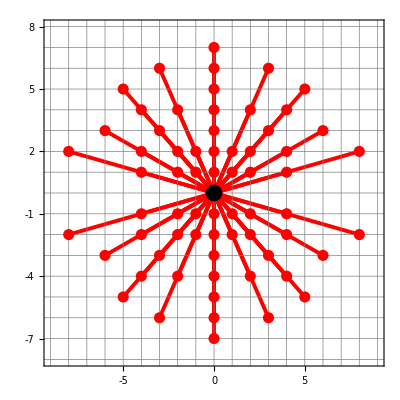

/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/bL_bT_plot.pdf

```mathematica
bLbTlist=MemDBGet[AmpDB,MemDBSelect[AmpDB,{}],{bL,bT}]//Union;
finalPlot1 = Graphics[{
{RGBColor[1,0.0,0.0],Thickness[0.007],Line[{{0,0},#}]&/@bLbTlist},
{Red,PointSize[0.02],Point[bLbTlist]},
{Black,PointSize[0.03],Point[{0,0}]}},
Axes->True,FrameLabel->{"",""}, BaseStyle->{FontSize->18},GridLines->{Range[-10,10],Range[-10,10]},GridLinesStyle->Directive[Gray],Ticks->{Range[-10,10],Range[-10,10]},AspectRatio->1,PlotRange->{{-9,9},{-8,8}},Frame->True]
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/bL_bT_plot.pdf",finalPlot1]
```

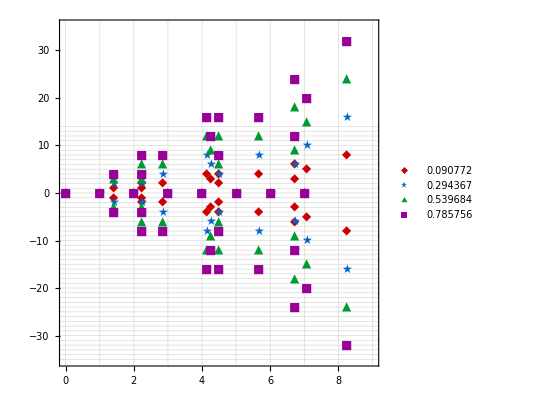

/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/Pb_bsq_plot.pdf

```mathematica
plValues={-1,-2,-3,-4};
zetaValues={0.090772,0.294367,0.539684,0.785756};
markers={"◆","★","▲","■"};
colors={RGBColor[0.8,0,0],RGBColor[0,0.4,0.8],RGBColor[0,0.6,0.2],RGBColor[0.6,0,0.6]};
plotPrimitives=Table[Module[{bPbsqlist,bPblist},bPbsqlist=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{PL->plValues[[i]]}],{Pb32by2Pi,bsquare}]//Union;
bPblist=bPbsqlist/. {p_,b2_}:>{Sqrt[b2],p};
{colors[[i]],Thickness[0.003],Text[Style[markers[[i]],12],#]&/@bPblist}],{i,1,4}];
mainPlot=Graphics[{plotPrimitives},Axes->True,AxesLabel->{},GridLines->{Range[0,9],Range[-35,35]},GridLinesStyle->Directive[LightGray],PlotRange->{{0,9},{-35,35}},FrameLabel->{"",""},BaseStyle->{FontSize->18},AspectRatio->1,Frame->True];
finalPlot2=Legended[mainPlot,PointLegend[colors,Row[{" ",#}]&/@zetaValues,LabelStyle->Directive[FontSize->18],LegendMarkers->({#,12}&/@markers)]]
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/Pb_bsq_plot.pdf",finalPlot2]
```

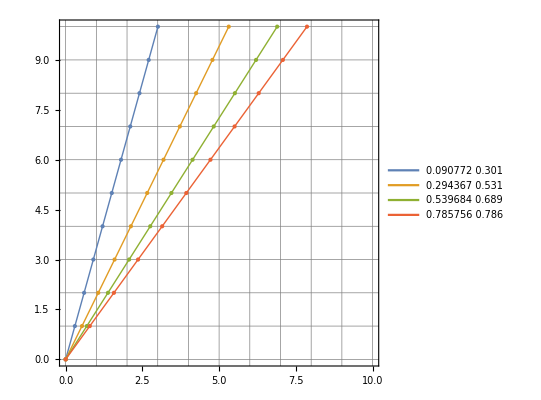

/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/v1_v2_allzetahat_plot.pdf

```mathematica
meanfromJK[JKvalue_]:=Module[{meanvalue},
meanvalue = MakeErrBars[{{1,JKvalue}}][[1]][[1]][[2]];
Return[meanvalue];
];
etavalue=10;
dbNoList={1,2,3,4};
colors={ColorData[97,1],ColorData[97,2],ColorData[97,3],ColorData[97,4]};
allPlotElements={};
legendLabels={};
(*Loop through all dbNo values*)
Do[dbNo=dbNoList[[dbIdx]];
c=colors[[dbIdx]];
platdb=BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_"<>ToString[dbNo]<>"/UminusD_Plateaus_jn.bidatex"];
NEdb=BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_"<>ToString[dbNo]<>"/NucleonEnergy_jn.bidatex"];
P0=MemDBGet[NEdb,MemDBSelect[NEdb,{}],energy][[1]];
II=(P0/P0);
P1=dbNo*II*((2*Pi)/(32));
Msquare=(P0*P0)-(P1*P1);
M=Sqrt[Msquare];
ztahat=Sqrt[(P1*P1)/(M*M*(((M*M)/(P1*P1))+(2*II)))];
(*Append the meanfromJK[ztahat] calculation to the legend list*)
Rztahatsquare=II-Sqrt[II+(II/(ztahat*ztahat))];
v1byv3jakk=(M*ztahat)/(Sqrt[(P1*P1)-(M*M*ztahat*ztahat)]);
v1BYv3=Abs[MakeErrBars[{{1,v1byv3jakk}}][[1]][[1]][[2]]];
v1[v3_]:=v3*v1BYv3;AppendTo[legendLabels,Style[Row[{" ",meanfromJK[ztahat]," ",Round[v1BYv3,0.001]}],18]];
(*Generate ONLY the theoretical vvector*)vvector=Table[{v1[v3],0,v3},{v3,0,etavalue}];
(*Store ONLY the solid line and points for this dbNo*)AppendTo[allPlotElements,{c,PointSize[Large],Point[vvector[[All,{1,3}]]],c,Thick,Line[vvector[[All,{1,3}]]]}];,{dbIdx,Length[dbNoList]}];
(*Draw the combined Graphics and attach the LineLegend*)
finalPlot3=Legended[Graphics[allPlotElements,Axes->True,FrameLabel->{"",""},BaseStyle->{FontSize->18},GridLines->{Range[0,16],Range[0,14]},GridLinesStyle->Directive[Gray],PlotRange->{{0,10},{0,10}},Frame->True],LineLegend[colors,legendLabels]]
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/v1_v2_allzetahat_plot.pdf",finalPlot3]
```

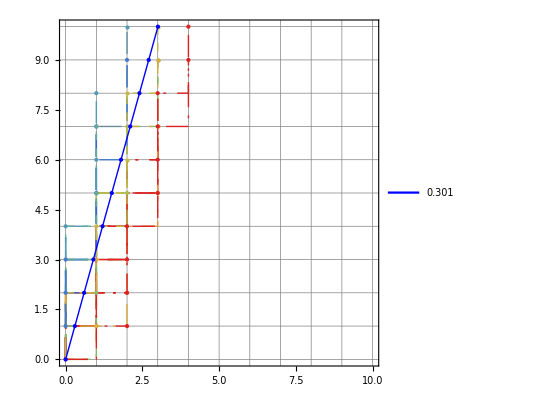

| Gauge-link paths for interpolation ( 0.090772)
0(0.301,0,1) | {{}}
1(0.301,0,1) | {{3},{1,3},{3,1},{1,3,1}}
2(0.301,0,1) | {{3,3},{3,1,3},{1,3,1,3},{3,1,3,1}}
3(0.301,0,1) | {{3,3,3},{3,1,3,3},{3,3,1,3},{3,1,3,1,3}}
4(0.301,0,1) | {{3,3,3,3},{3,3,1,3,3},{3,1,3,3,1,3}}
5(0.301,0,1) | {{3,3,1,3,3,3},{3,3,3,1,3,3},{3,3,1,3,1,3,3},{3,1,3,1,3,3,1,3},{3,1,3,3,1,3,1,3}}
6(0.301,0,1) | {{3,3,3,1,3,3,3},{3,3,1,3,3,1,3,3},{3,1,3,3,1,3,3,1,3}}
7(0.301,0,1) | {{3,3,3,1,3,3,3,3},{3,3,3,3,1,3,3,3},{3,3,1,3,3,3,1,3,3},{3,3,1,3,1,3,3,1,3,3},{3,3,1,3,3,1,3,1,3,3}}
8(0.301,0,1) | {{3,3,3,3,1,3,3,3,3},{3,3,3,1,3,3,1,3,3,3},{3,3,1,3,3,1,3,3,1,3,3}}
9(0.301,0,1) | {{3,3,3,1,3,3,3,1,3,3,3},{3,3,1,3,3,1,3,3,3,1,3,3},{3,3,1,3,3,3,1,3,3,1,3,3},{3,3,1,3,3,1,3,1,3,3,1,3,3}}
10(0.301,0,1) | {{3,3,3,1,3,3,3,3,1,3,3,3},{3,3,1,3,3,3,1,3,3,3,1,3,3},{3,3,1,3,3,1,3,3,1,3,3,1,3,3}}

/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/v1_v2_withPath_forP-1_plot.pdf

/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/eta_gauge_links_forP-1_table.pdf

```mathematica
dbNo = 1;
etaValues=Range[10,0,-1];
maxEta=Max[etaValues];
platdb=BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_"<>ToString[dbNo]<>"/UminusD_Plateaus_jn.bidatex"];
NEdb=BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_"<>ToString[dbNo]<>"/NucleonEnergy_jn.bidatex"];
P0=MemDBGet[NEdb,MemDBSelect[NEdb,{}],energy][[1]];(*P0=EN*)II=(P0/P0);
P1=dbNo*II*((2*Pi)/(32));(*P1= |P1|*)Msquare=(P0*P0)-(P1*P1);
M=Sqrt[Msquare];
ztahat=Sqrt[(P1*P1)/(M*M*(((M*M)/(P1*P1))+(2*II)))];
Rztahatsquare=II-Sqrt[II+(II/(ztahat*ztahat))];
v1byv3jakk=(M*ztahat)/(Sqrt[(P1*P1)-(M*M*ztahat*ztahat)]);
v1BYv3=Abs[MakeErrBars[{{1,v1byv3jakk}}][[1]][[1]][[2]]];
v1[v3_]:=v3*v1BYv3;
PathToLinks[sidelink_]:=(ULinkslist={};
AppendTo[ULinkslist,{0,0,0}];
Do[linki=sidelink[[i]];
If[linki==1,AppendTo[ULinkslist,{ULinkslist[[i]][[1]]+1,ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]}]];
If[linki==3,AppendTo[ULinkslist,{ULinkslist[[i]][[1]],ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]+1}]];,{i,Length[sidelink]}];
Return[ULinkslist];)
vvector={};
Do[AppendTo[vvector,{v1[v3],0,v3}],{v3,0,maxEta}];

vlinksall=Union[MemDBGet[platdb,MemDBSelect[platdb,{numberFilter->Re}],sideLink]];
listsToRemove=Table[ConstantArray[1,i],{i,1,14}];
vlinks=Complement[vlinksall,listsToRemove];

allLatticeGraphics=Table[Module[{vlinksv3,latticevvector},vlinksv3=Select[vlinks,Count[#,3]==eta&];
latticevvector=Table[PathToLinks[vlinksv3[[variousv]]],{variousv,Length[vlinksv3]}];
If[Length[latticevvector]>0,Table[{ColorData["Rainbow"][i/Length[latticevvector]],Thick,Dashing[Switch[Mod[i,4,1],1,{0.04,0.02},2,{0.015,0.015},3,{0.04,0.02,0.005,0.02},4,{0.04,0.015,0.005,0.015}]],Line[latticevvector[[i]][[All,{1,3}]]],PointSize[Large],Point[Last[latticevvector[[i]][[All,{1,3}]]]] },{i,Length[latticevvector]}],{} ]],{eta,etaValues}];

mainPlot = Graphics[{allLatticeGraphics,Blue,PointSize[Large],Point[vvector[[All,{1,3}]]],Blue,Thick,Line[vvector[[All,{1,3}]]]},Axes->True,FrameLabel->{"",""},BaseStyle->{FontSize->18},GridLines->{Range[0,16],Range[0,14]},GridLinesStyle->Directive[Gray],PlotRange->{{0,10},{0,10}},Frame->True];
finalPlot=Legended[mainPlot,Column[{Style[Row[{" ",meanfromJK[ztahat]}],18],LineLegend[{Directive[Blue,Thick]},{Row[{"",Round[v1BYv3,0.001]}]},LabelStyle->18],PointLegend[{Blue},{""},LegendMarkers->{"●"},LabelStyle->18]}]]
(* ==========================================*)(*Extract and Format the Table Data*)(* ==========================================*)
ascendingEtaValues=Sort[etaValues];
(*tableData=Table[{eta,Select[vlinks,Count[#,3]==eta&]},{eta,ascendingEtaValues}];*)
tableData=Table[{Row[{eta,"(",Round[v1BYv3,0.001],",0,1)"}],Select[vlinks,Count[#,3]==eta&]},{eta,ascendingEtaValues}];
tableWithHeaders=Prepend[tableData,{Style["",16],Style[Row[{"Gauge-link paths for interpolation ( ",meanfromJK[ztahat],")"}],16]}];
formattedTable=Grid[tableWithHeaders,Frame->All,Background->{None,{LightGray,None}},(*Highlights the header row*)Alignment->{Center,Center},Spacings->{3,2},BaseStyle->{FontSize->14},ItemSize->{{10,70},Automatic}];
Print[formattedTable]
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/v1_v2_withPath_forP-" <> ToString[dbNo] <> "_plot.pdf",finalPlot]
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/eta_gauge_links_forP-" <> ToString[dbNo] <> "_table.pdf",formattedTable]
```

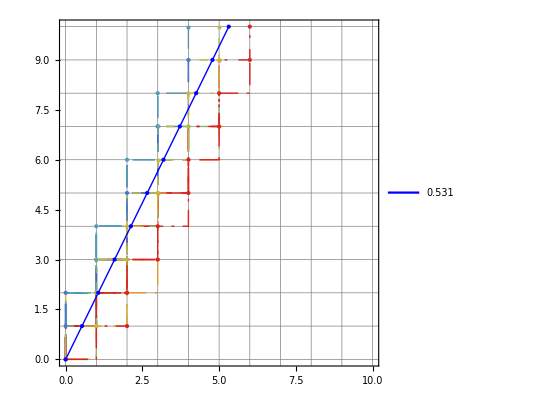

| Gauge-link paths for interpolation ( 0.294367)
0(0.531,0,1) | {{}}
1(0.531,0,1) | {{3},{1,3},{3,1},{1,3,1}}
2(0.531,0,1) | {{3,3},{3,1,3},{1,3,1,3},{3,1,3,1}}
3(0.531,0,1) | {{3,1,3,3},{3,3,1,3},{3,1,3,1,3},{1,3,1,3,1,3},{3,1,3,1,3,1}}
4(0.531,0,1) | {{3,3,1,3,3},{3,1,3,3,1,3},{3,1,3,1,3,1,3}}
5(0.531,0,1) | {{3,3,1,3,1,3,3},{3,1,3,1,3,3,1,3},{3,1,3,3,1,3,1,3},{3,1,3,1,3,1,3,1,3}}
6(0.531,0,1) | {{3,3,1,3,3,1,3,3},{3,1,3,3,1,3,3,1,3},{3,1,3,1,3,3,1,3,1,3}}
7(0.531,0,1) | {{3,3,1,3,1,3,3,1,3,3},{3,3,1,3,3,1,3,1,3,3},{3,1,3,3,1,3,1,3,3,1,3},{3,1,3,1,3,1,3,3,1,3,1,3},{3,1,3,1,3,3,1,3,1,3,1,3}}
8(0.531,0,1) | {{3,3,1,3,3,1,3,3,1,3,3},{3,1,3,3,1,3,3,1,3,3,1,3},{3,1,3,3,1,3,1,3,1,3,3,1,3}}
9(0.531,0,1) | {{3,3,1,3,3,1,3,1,3,3,1,3,3},{3,1,3,3,1,3,1,3,3,1,3,1,3,3},{3,3,1,3,1,3,3,1,3,1,3,3,1,3},{3,1,3,1,3,3,1,3,1,3,3,1,3,1,3}}
10(0.531,0,1) | {{3,3,1,3,3,1,3,3,1,3,3,1,3,3},{3,1,3,3,1,3,3,1,3,3,1,3,3,1,3},{3,1,3,3,1,3,1,3,3,1,3,1,3,3,1,3}}

/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/v1_v2_withPath_forP-2_plot.pdf

/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/eta_gauge_links_forP-2_table.pdf

```mathematica
dbNo = 2;
etaValues=Range[10,0,-1];
maxEta=Max[etaValues];
platdb=BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_"<>ToString[dbNo]<>"/UminusD_Plateaus_jn.bidatex"];
NEdb=BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_"<>ToString[dbNo]<>"/NucleonEnergy_jn.bidatex"];
P0=MemDBGet[NEdb,MemDBSelect[NEdb,{}],energy][[1]];(*P0=EN*)II=(P0/P0);
P1=dbNo*II*((2*Pi)/(32));(*P1= |P1|*)Msquare=(P0*P0)-(P1*P1);
M=Sqrt[Msquare];
ztahat=Sqrt[(P1*P1)/(M*M*(((M*M)/(P1*P1))+(2*II)))];
Rztahatsquare=II-Sqrt[II+(II/(ztahat*ztahat))];
v1byv3jakk=(M*ztahat)/(Sqrt[(P1*P1)-(M*M*ztahat*ztahat)]);
v1BYv3=Abs[MakeErrBars[{{1,v1byv3jakk}}][[1]][[1]][[2]]];
v1[v3_]:=v3*v1BYv3;
PathToLinks[sidelink_]:=(ULinkslist={};
AppendTo[ULinkslist,{0,0,0}];
Do[linki=sidelink[[i]];
If[linki==1,AppendTo[ULinkslist,{ULinkslist[[i]][[1]]+1,ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]}]];
If[linki==3,AppendTo[ULinkslist,{ULinkslist[[i]][[1]],ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]+1}]];,{i,Length[sidelink]}];
Return[ULinkslist];)
vvector={};
Do[AppendTo[vvector,{v1[v3],0,v3}],{v3,0,maxEta}];

vlinksall=Union[MemDBGet[platdb,MemDBSelect[platdb,{numberFilter->Re}],sideLink]];
listsToRemove=Table[ConstantArray[1,i],{i,1,14}];
vlinks=Complement[vlinksall,listsToRemove];

allLatticeGraphics=Table[Module[{vlinksv3,latticevvector},vlinksv3=Select[vlinks,Count[#,3]==eta&];
latticevvector=Table[PathToLinks[vlinksv3[[variousv]]],{variousv,Length[vlinksv3]}];
If[Length[latticevvector]>0,Table[{ColorData["Rainbow"][i/Length[latticevvector]],Thick,Dashing[Switch[Mod[i,4,1],1,{0.04,0.02},2,{0.015,0.015},3,{0.04,0.02,0.005,0.02},4,{0.04,0.015,0.005,0.015}]],Line[latticevvector[[i]][[All,{1,3}]]],PointSize[Large],Point[Last[latticevvector[[i]][[All,{1,3}]]]] },{i,Length[latticevvector]}],{} ]],{eta,etaValues}];

mainPlot = Graphics[{allLatticeGraphics,Blue,PointSize[Large],Point[vvector[[All,{1,3}]]],Blue,Thick,Line[vvector[[All,{1,3}]]]},Axes->True,FrameLabel->{"",""},BaseStyle->{FontSize->18},GridLines->{Range[0,16],Range[0,14]},GridLinesStyle->Directive[Gray],PlotRange->{{0,10},{0,10}},Frame->True];
finalPlot=Legended[mainPlot,Column[{Style[Row[{" ",meanfromJK[ztahat]}],18],LineLegend[{Directive[Blue,Thick]},{Row[{"",Round[v1BYv3,0.001]}]},LabelStyle->18],PointLegend[{Blue},{""},LegendMarkers->{"●"},LabelStyle->18]}]]
(* ==========================================*)(*Extract and Format the Table Data*)(* ==========================================*)
ascendingEtaValues=Sort[etaValues];
(*tableData=Table[{eta,Select[vlinks,Count[#,3]==eta&]},{eta,ascendingEtaValues}];*)
tableData=Table[{Row[{eta,"(",Round[v1BYv3,0.001],",0,1)"}],Select[vlinks,Count[#,3]==eta&]},{eta,ascendingEtaValues}];
tableWithHeaders=Prepend[tableData,{Style["",16],Style[Row[{"Gauge-link paths for interpolation ( ",meanfromJK[ztahat],")"}],16]}];
formattedTable=Grid[tableWithHeaders,Frame->All,Background->{None,{LightGray,None}},(*Highlights the header row*)Alignment->{Center,Center},Spacings->{3,2},BaseStyle->{FontSize->14},ItemSize->{{10,70},Automatic}];
Print[formattedTable]
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/v1_v2_withPath_forP-" <> ToString[dbNo] <> "_plot.pdf",finalPlot]
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/eta_gauge_links_forP-" <> ToString[dbNo] <> "_table.pdf",formattedTable]
```

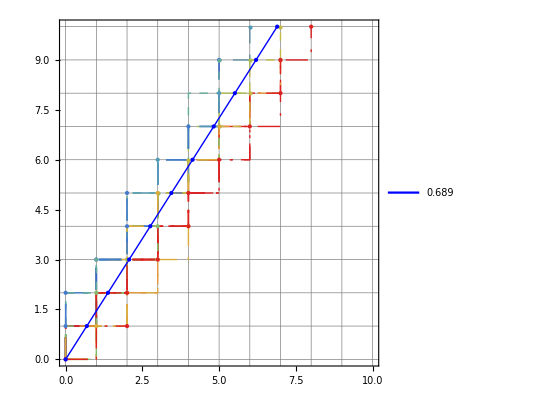

| Gauge-link paths for interpolation ( 0.539684)
0(0.689,0,1) | {{}}
1(0.689,0,1) | {{3},{1,3},{3,1},{1,3,1}}
2(0.689,0,1) | {{3,3},{3,1,3},{1,3,1,3},{3,1,3,1}}
3(0.689,0,1) | {{3,1,3,3},{3,3,1,3},{3,1,3,1,3},{1,3,1,3,1,3},{3,1,3,1,3,1}}
4(0.689,0,1) | {{3,1,3,3,1,3},{3,1,3,1,3,1,3},{1,3,1,3,1,3,1,3},{3,1,3,1,3,1,3,1}}
5(0.689,0,1) | {{3,3,1,3,1,3,3},{3,1,3,1,3,3,1,3},{3,1,3,3,1,3,1,3},{3,1,3,1,3,1,3,1,3}}
6(0.689,0,1) | {{3,1,3,3,1,3,3,1,3},{3,1,3,1,3,3,1,3,1,3},{3,1,3,1,3,1,3,1,3,1,3}}
7(0.689,0,1) | {{3,1,3,3,1,3,1,3,3,1,3},{3,1,3,1,3,1,3,3,1,3,1,3},{3,1,3,1,3,3,1,3,1,3,1,3},{3,1,3,1,3,1,3,1,3,1,3,1,3}}
8(0.689,0,1) | {{3,1,3,3,1,3,1,3,1,3,3,1,3},{3,1,3,1,3,1,3,3,1,3,1,3,1,3},{3,1,3,1,3,1,3,1,3,1,3,1,3,1,3}}
9(0.689,0,1) | {{3,1,3,3,1,3,1,3,3,1,3,1,3,3},{3,3,1,3,1,3,3,1,3,1,3,3,1,3},{3,1,3,1,3,3,1,3,1,3,3,1,3,1,3},{3,1,3,1,3,1,3,1,3,3,1,3,1,3,1,3},{3,1,3,1,3,1,3,3,1,3,1,3,1,3,1,3}}
10(0.689,0,1) | {{3,1,3,3,1,3,1,3,3,1,3,1,3,3,1,3},{3,1,3,1,3,3,1,3,1,3,1,3,3,1,3,1,3},{3,1,3,1,3,1,3,1,3,3,1,3,1,3,1,3,1,3}}

/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/v1_v2_withPath_forP-3_plot.pdf

/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/eta_gauge_links_forP-3_table.pdf

```mathematica
dbNo = 3;
etaValues=Range[10,0,-1];
etaValues=Range[10,0,-1];
maxEta=Max[etaValues];
platdb=BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_"<>ToString[dbNo]<>"/UminusD_Plateaus_jn.bidatex"];
NEdb=BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_"<>ToString[dbNo]<>"/NucleonEnergy_jn.bidatex"];
P0=MemDBGet[NEdb,MemDBSelect[NEdb,{}],energy][[1]];(*P0=EN*)II=(P0/P0);
P1=dbNo*II*((2*Pi)/(32));(*P1= |P1|*)Msquare=(P0*P0)-(P1*P1);
M=Sqrt[Msquare];
ztahat=Sqrt[(P1*P1)/(M*M*(((M*M)/(P1*P1))+(2*II)))];
Rztahatsquare=II-Sqrt[II+(II/(ztahat*ztahat))];
v1byv3jakk=(M*ztahat)/(Sqrt[(P1*P1)-(M*M*ztahat*ztahat)]);
v1BYv3=Abs[MakeErrBars[{{1,v1byv3jakk}}][[1]][[1]][[2]]];
v1[v3_]:=v3*v1BYv3;
PathToLinks[sidelink_]:=(ULinkslist={};
AppendTo[ULinkslist,{0,0,0}];
Do[linki=sidelink[[i]];
If[linki==1,AppendTo[ULinkslist,{ULinkslist[[i]][[1]]+1,ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]}]];
If[linki==3,AppendTo[ULinkslist,{ULinkslist[[i]][[1]],ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]+1}]];,{i,Length[sidelink]}];
Return[ULinkslist];)
vvector={};
Do[AppendTo[vvector,{v1[v3],0,v3}],{v3,0,maxEta}];

vlinksall=Union[MemDBGet[platdb,MemDBSelect[platdb,{numberFilter->Re}],sideLink]];
listsToRemove=Table[ConstantArray[1,i],{i,1,14}];
vlinks=Complement[vlinksall,listsToRemove];

allLatticeGraphics=Table[Module[{vlinksv3,latticevvector},vlinksv3=Select[vlinks,Count[#,3]==eta&];
latticevvector=Table[PathToLinks[vlinksv3[[variousv]]],{variousv,Length[vlinksv3]}];
If[Length[latticevvector]>0,Table[{ColorData["Rainbow"][i/Length[latticevvector]],Thick,Dashing[Switch[Mod[i,4,1],1,{0.04,0.02},2,{0.015,0.015},3,{0.04,0.02,0.005,0.02},4,{0.04,0.015,0.005,0.015}]],Line[latticevvector[[i]][[All,{1,3}]]],PointSize[Large],Point[Last[latticevvector[[i]][[All,{1,3}]]]] },{i,Length[latticevvector]}],{} ]],{eta,etaValues}];

mainPlot = Graphics[{allLatticeGraphics,Blue,PointSize[Large],Point[vvector[[All,{1,3}]]],Blue,Thick,Line[vvector[[All,{1,3}]]]},Axes->True,FrameLabel->{"",""},BaseStyle->{FontSize->18},GridLines->{Range[0,16],Range[0,14]},GridLinesStyle->Directive[Gray],PlotRange->{{0,10},{0,10}},Frame->True];
finalPlot=Legended[mainPlot,Column[{Style[Row[{" ",meanfromJK[ztahat]}],18],LineLegend[{Directive[Blue,Thick]},{Row[{"",Round[v1BYv3,0.001]}]},LabelStyle->18],PointLegend[{Blue},{""},LegendMarkers->{"●"},LabelStyle->18]}]]
(* ==========================================*)(*Extract and Format the Table Data*)(* ==========================================*)
ascendingEtaValues=Sort[etaValues];
(*tableData=Table[{eta,Select[vlinks,Count[#,3]==eta&]},{eta,ascendingEtaValues}];*)
tableData=Table[{Row[{eta,"(",Round[v1BYv3,0.001],",0,1)"}],Select[vlinks,Count[#,3]==eta&]},{eta,ascendingEtaValues}];
tableWithHeaders=Prepend[tableData,{Style["",16],Style[Row[{"Gauge-link paths for interpolation ( ",meanfromJK[ztahat],")"}],16]}];
formattedTable=Grid[tableWithHeaders,Frame->All,Background->{None,{LightGray,None}},(*Highlights the header row*)Alignment->{Center,Center},Spacings->{3,2},BaseStyle->{FontSize->14},ItemSize->{{10,70},Automatic}];
Print[formattedTable]
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/v1_v2_withPath_forP-" <> ToString[dbNo] <> "_plot.pdf",finalPlot]
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/eta_gauge_links_forP-" <> ToString[dbNo] <> "_table.pdf",formattedTable]
```

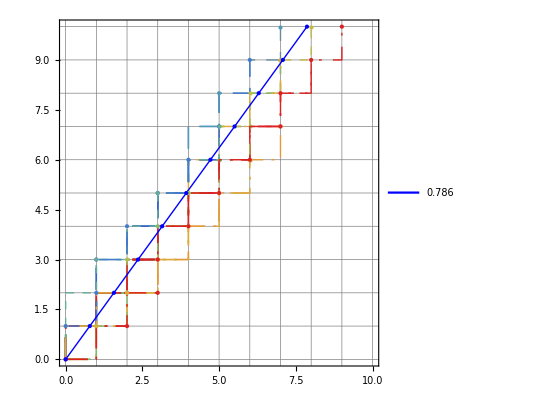

| Gauge-link paths for interpolation ( 0.785756)
0(0.786,0,1) | {{}}
1(0.786,0,1) | {{3},{1,3},{3,1},{1,3,1}}
2(0.786,0,1) | {{3,1,3},{1,3,1,3},{3,1,3,1},{1,3,1,3,1}}
3(0.786,0,1) | {{3,1,3,3},{3,3,1,3},{3,1,3,1,3},{1,3,1,3,1,3},{3,1,3,1,3,1}}
4(0.786,0,1) | {{3,1,3,3,1,3},{3,1,3,1,3,1,3},{1,3,1,3,1,3,1,3},{3,1,3,1,3,1,3,1}}
5(0.786,0,1) | {{3,1,3,1,3,3,1,3},{3,1,3,3,1,3,1,3},{3,1,3,1,3,1,3,1,3},{1,3,1,3,1,3,1,3,1,3},{3,1,3,1,3,1,3,1,3,1}}
6(0.786,0,1) | {{3,1,3,1,3,3,1,3,1,3},{3,1,3,1,3,1,3,1,3,1,3},{1,3,1,3,1,3,1,3,1,3,1,3},{3,1,3,1,3,1,3,1,3,1,3,1}}
7(0.786,0,1) | {{3,1,3,1,3,1,3,3,1,3,1,3},{3,1,3,1,3,3,1,3,1,3,1,3},{3,1,3,1,3,1,3,1,3,1,3,1,3},{1,3,1,3,1,3,1,3,1,3,1,3,1,3},{3,1,3,1,3,1,3,1,3,1,3,1,3,1}}
8(0.786,0,1) | {{3,1,3,3,1,3,1,3,1,3,3,1,3},{3,1,3,1,3,1,3,3,1,3,1,3,1,3},{3,1,3,1,3,1,3,1,3,1,3,1,3,1,3}}
9(0.786,0,1) | {{3,1,3,1,3,3,1,3,1,3,3,1,3,1,3},{3,1,3,1,3,1,3,1,3,3,1,3,1,3,1,3},{3,1,3,1,3,1,3,3,1,3,1,3,1,3,1,3},{3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3}}
10(0.786,0,1) | {{3,1,3,1,3,3,1,3,1,3,1,3,3,1,3,1,3},{3,1,3,1,3,1,3,1,3,3,1,3,1,3,1,3,1,3},{3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3}}

/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/v1_v2_withPath_forP-4_plot.pdf

/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/eta_gauge_links_forP-4_table.pdf

```mathematica
dbNo = 4;
etaValues=Range[10,0,-1];
maxEta=Max[etaValues];
platdb=BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_"<>ToString[dbNo]<>"/UminusD_Plateaus_jn.bidatex"];
NEdb=BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_"<>ToString[dbNo]<>"/NucleonEnergy_jn.bidatex"];
P0=MemDBGet[NEdb,MemDBSelect[NEdb,{}],energy][[1]];(*P0=EN*)II=(P0/P0);
P1=dbNo*II*((2*Pi)/(32));(*P1= |P1|*)Msquare=(P0*P0)-(P1*P1);
M=Sqrt[Msquare];
ztahat=Sqrt[(P1*P1)/(M*M*(((M*M)/(P1*P1))+(2*II)))];
Rztahatsquare=II-Sqrt[II+(II/(ztahat*ztahat))];
v1byv3jakk=(M*ztahat)/(Sqrt[(P1*P1)-(M*M*ztahat*ztahat)]);
v1BYv3=Abs[MakeErrBars[{{1,v1byv3jakk}}][[1]][[1]][[2]]];
v1[v3_]:=v3*v1BYv3;
PathToLinks[sidelink_]:=(ULinkslist={};
AppendTo[ULinkslist,{0,0,0}];
Do[linki=sidelink[[i]];
If[linki==1,AppendTo[ULinkslist,{ULinkslist[[i]][[1]]+1,ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]}]];
If[linki==3,AppendTo[ULinkslist,{ULinkslist[[i]][[1]],ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]+1}]];,{i,Length[sidelink]}];
Return[ULinkslist];)
vvector={};
Do[AppendTo[vvector,{v1[v3],0,v3}],{v3,0,maxEta}];

vlinksall=Union[MemDBGet[platdb,MemDBSelect[platdb,{numberFilter->Re}],sideLink]];
listsToRemove=Table[ConstantArray[1,i],{i,1,14}];
vlinks=Complement[vlinksall,listsToRemove];

allLatticeGraphics=Table[Module[{vlinksv3,latticevvector},vlinksv3=Select[vlinks,Count[#,3]==eta&];
latticevvector=Table[PathToLinks[vlinksv3[[variousv]]],{variousv,Length[vlinksv3]}];
If[Length[latticevvector]>0,Table[{ColorData["Rainbow"][i/Length[latticevvector]],Thick,Dashing[Switch[Mod[i,4,1],1,{0.04,0.02},2,{0.015,0.015},3,{0.04,0.02,0.005,0.02},4,{0.04,0.015,0.005,0.015}]],Line[latticevvector[[i]][[All,{1,3}]]],PointSize[Large],Point[Last[latticevvector[[i]][[All,{1,3}]]]] },{i,Length[latticevvector]}],{} ]],{eta,etaValues}];

mainPlot = Graphics[{allLatticeGraphics,Blue,PointSize[Large],Point[vvector[[All,{1,3}]]],Blue,Thick,Line[vvector[[All,{1,3}]]]},Axes->True,FrameLabel->{"",""},BaseStyle->{FontSize->18},GridLines->{Range[0,16],Range[0,14]},GridLinesStyle->Directive[Gray],PlotRange->{{0,10},{0,10}},Frame->True];
finalPlot=Legended[mainPlot,Column[{Style[Row[{" ",meanfromJK[ztahat]}],18],LineLegend[{Directive[Blue,Thick]},{Row[{"",Round[v1BYv3,0.001]}]},LabelStyle->18],PointLegend[{Blue},{""},LegendMarkers->{"●"},LabelStyle->18]}]]
(* ==========================================*)(*Extract and Format the Table Data*)(* ==========================================*)
ascendingEtaValues=Sort[etaValues];
(*tableData=Table[{eta,Select[vlinks,Count[#,3]==eta&]},{eta,ascendingEtaValues}];*)
tableData=Table[{Row[{eta,"(",Round[v1BYv3,0.001],",0,1)"}],Select[vlinks,Count[#,3]==eta&]},{eta,ascendingEtaValues}];
tableWithHeaders=Prepend[tableData,{Style["",16],Style[Row[{"Gauge-link paths for interpolation ( ",meanfromJK[ztahat],")"}],16]}];
formattedTable=Grid[tableWithHeaders,Frame->All,Background->{None,{LightGray,None}},(*Highlights the header row*)Alignment->{Center,Center},Spacings->{3,2},BaseStyle->{FontSize->14},ItemSize->{{10,70},Automatic}];
Print[formattedTable]
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/v1_v2_withPath_forP-" <> ToString[dbNo] <> "_plot.pdf",finalPlot]
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/eta_gauge_links_forP-" <> ToString[dbNo] <> "_table.pdf",formattedTable]
```

```mathematica
dbNo = 1;
etaValues=Range[10,1,-1];
maxEta=Max[etaValues];
platdb=BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_"<>ToString[dbNo]<>"/UminusD_Plateaus_jn.bidatex"];
NEdb=BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_"<>ToString[dbNo]<>"/NucleonEnergy_jn.bidatex"];
P0=MemDBGet[NEdb,MemDBSelect[NEdb,{}],energy][[1]];(*P0=EN*)II=(P0/P0);
P1=dbNo*II*((2*Pi)/(32));(*P1= |P1|*)Msquare=(P0*P0)-(P1*P1);
M=Sqrt[Msquare];
ztahat=Sqrt[(P1*P1)/(M*M*(((M*M)/(P1*P1))+(2*II)))];
Rztahatsquare=II-Sqrt[II+(II/(ztahat*ztahat))];
v1byv3jakk=(M*ztahat)/(Sqrt[(P1*P1)-(M*M*ztahat*ztahat)]);
v1BYv3=Abs[MakeErrBars[{{1,v1byv3jakk}}][[1]][[1]][[2]]];
v1[v3_]:=v3*v1BYv3;
AllLinkPathList = MemDBGet[platdb,MemDBSelect[platdb,{}],linkPath];
DistinctLinkPaths= DeleteDuplicates[AllLinkPathList];
bveclinkPathsideNumLIST={};
Do[
AppendTo[bveclinkPathsideNumLIST,{PathToShift[DistinctLinkPaths[[i]],3],DistinctLinkPaths[[i]]}],{i,CountDistinct[AllLinkPathList]}] (* i+1 is to skipp linkPath {} *)

(*Run this AFTER your Do loop*)bveclinkPathsideNumLIST=KeyValueMap[List,GroupBy[bveclinkPathsideNumLIST,First->Last]];
bveclinkPathsideNumLISTforbpositive1=Select[bveclinkPathsideNumLIST,(#[[1,1]]==0)&];
bveclinkPathsideNumLISTforbpositive2=Select[bveclinkPathsideNumLIST,#[[1,1]]>0&];
bveclinkPathsideNumLISTforbpositive3=Select[bveclinkPathsideNumLIST,#[[1,1]]<0&];

bveclinkPathsideNumLISTforbnegative1=Select[bveclinkPathsideNumLIST,(#[[1,1]]==0)&];
bveclinkPathsideNumLISTforbnegative2=Select[bveclinkPathsideNumLIST,#[[1,1]]<0&];
bveclinkPathsideNumLISTforbnegative3=Select[bveclinkPathsideNumLIST,#[[1,1]]>0&];

(*1. Define Headers*)
headerPosVec=Style["",14];
headerNegVec=Style["",14];
headerPath=Style["Gauge-link paths",14];
maxLen=Max[Length[bveclinkPathsideNumLISTforbpositive1],Length[bveclinkPathsideNumLISTforbnegative1]];
paddedPos=PadRight[bveclinkPathsideNumLISTforbpositive1,maxLen,{{"",""}}];
paddedNeg=PadRight[bveclinkPathsideNumLISTforbnegative1,maxLen,{{"",""}}];
combinedData=Table[Join[paddedPos[[i]],paddedNeg[[i]]],{i,maxLen}];
tableData=Prepend[combinedData,{headerPosVec,headerPath,headerNegVec,headerPath}];
formattedTable=Grid[tableData,Frame->True,Background->{None,{LightGray,None}},Alignment->Center,Spacings->{2,1.5},Dividers->{{True,True,Directive[AbsoluteThickness[3],Black],True,True},(*Vertical lines*)All (*Horizontal lines*)}];
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/b_gauge_links_for_table1.pdf",formattedTable];
Print[formattedTable]

maxLen=Max[Length[bveclinkPathsideNumLISTforbpositive2],Length[bveclinkPathsideNumLISTforbnegative2]];
paddedPos=PadRight[bveclinkPathsideNumLISTforbpositive2,maxLen,{{"",""}}];
paddedNeg=PadRight[bveclinkPathsideNumLISTforbnegative2,maxLen,{{"",""}}];
combinedData=Table[Join[paddedPos[[i]],paddedNeg[[i]]],{i,maxLen}];
tableData=Prepend[combinedData,{headerPosVec,headerPath,headerNegVec,headerPath}];
formattedTable=Grid[tableData,Frame->True,Background->{None,{LightGray,None}},Alignment->Center,Spacings->{2,1.5},Dividers->{{True,True,Directive[AbsoluteThickness[3],Black],True,True},(*Vertical lines*)All (*Horizontal lines*)}];
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/b_gauge_links_for_table2.pdf",formattedTable];
Print[formattedTable]

maxLen=Max[Length[bveclinkPathsideNumLISTforbpositive3],Length[bveclinkPathsideNumLISTforbnegative3]];
paddedPos=PadRight[bveclinkPathsideNumLISTforbpositive3,maxLen,{{"",""}}];
paddedNeg=PadRight[bveclinkPathsideNumLISTforbnegative3,maxLen,{{"",""}}];
combinedData=Table[Join[paddedPos[[i]],paddedNeg[[i]]],{i,maxLen}];
tableData=Prepend[combinedData,{headerPosVec,headerPath,headerNegVec,headerPath}];
formattedTable=Grid[tableData,Frame->True,Background->{None,{LightGray,None}},Alignment->Center,Spacings->{2,1.5},Dividers->{{True,True,Directive[AbsoluteThickness[3],Black],True,True},(*Vertical lines*)All (*Horizontal lines*)}];
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/b_gauge_links_for_table3.pdf",formattedTable];
Print[formattedTable]
```

| Gauge-link paths |  | Gauge-link paths
{0,0,0} | {{}} | {0,0,0} | {{}}
{0,1,0} | {{2}} | {0,1,0} | {{2}}
{0,2,0} | {{2,2}} | {0,2,0} | {{2,2}}
{0,3,0} | {{2,2,2}} | {0,3,0} | {{2,2,2}}
{0,4,0} | {{2,2,2,2}} | {0,4,0} | {{2,2,2,2}}
{0,5,0} | {{2,2,2,2,2}} | {0,5,0} | {{2,2,2,2,2}}
{0,6,0} | {{2,2,2,2,2,2}} | {0,6,0} | {{2,2,2,2,2,2}}
{0,7,0} | {{2,2,2,2,2,2,2}} | {0,7,0} | {{2,2,2,2,2,2,2}}
{0,-1,0} | {{-2}} | {0,-1,0} | {{-2}}
{0,-2,0} | {{-2,-2}} | {0,-2,0} | {{-2,-2}}
{0,-3,0} | {{-2,-2,-2}} | {0,-3,0} | {{-2,-2,-2}}
{0,-4,0} | {{-2,-2,-2,-2}} | {0,-4,0} | {{-2,-2,-2,-2}}
{0,-5,0} | {{-2,-2,-2,-2,-2}} | {0,-5,0} | {{-2,-2,-2,-2,-2}}
{0,-6,0} | {{-2,-2,-2,-2,-2,-2}} | {0,-6,0} | {{-2,-2,-2,-2,-2,-2}}
{0,-7,0} | {{-2,-2,-2,-2,-2,-2,-2}} | {0,-7,0} | {{-2,-2,-2,-2,-2,-2,-2}}

| Gauge-link paths |  | Gauge-link paths
{1,1,0} | {{2,1},{1,2}} | {-1,1,0} | {{2,-1},{-1,2}}
{2,2,0} | {{2,1,2,1},{1,2,1,2}} | {-2,2,0} | {{2,-1,2,-1},{-1,2,-1,2}}
{3,3,0} | {{2,1,2,1,2,1},{1,2,1,2,1,2}} | {-3,3,0} | {{2,-1,2,-1,2,-1},{-1,2,-1,2,-1,2}}
{4,4,0} | {{2,1,2,1,2,1,2,1},{1,2,1,2,1,2,1,2}} | {-4,4,0} | {{2,-1,2,-1,2,-1,2,-1},{-1,2,-1,2,-1,2,-1,2}}
{5,5,0} | {{2,1,2,1,2,1,2,1,2,1},{1,2,1,2,1,2,1,2,1,2}} | {-5,5,0} | {{2,-1,2,-1,2,-1,2,-1,2,-1},{-1,2,-1,2,-1,2,-1,2,-1,2}}
{1,2,0} | {{2,1,2}} | {-1,2,0} | {{2,-1,2}}
{2,4,0} | {{2,1,2,2,1,2}} | {-2,4,0} | {{2,-1,2,2,-1,2}}
{3,6,0} | {{2,1,2,2,1,2,2,1,2}} | {-3,6,0} | {{2,-1,2,2,-1,2,2,-1,2}}
{2,1,0} | {{1,2,1}} | {-2,1,0} | {{-1,2,-1}}
{4,2,0} | {{1,2,1,1,2,1}} | {-4,2,0} | {{-1,2,-1,-1,2,-1}}
{6,3,0} | {{1,2,1,1,2,1,1,2,1}} | {-6,3,0} | {{-1,2,-1,-1,2,-1,-1,2,-1}}
{4,1,0} | {{1,1,2,1,1}} | {-4,1,0} | {{-1,-1,2,-1,-1}}
{8,2,0} | {{1,1,2,1,1,1,1,2,1,1}} | {-8,2,0} | {{-1,-1,2,-1,-1,-1,-1,2,-1,-1}}
{1,-1,0} | {{-2,1},{1,-2}} | {-1,-1,0} | {{-2,-1},{-1,-2}}
{2,-2,0} | {{-2,1,-2,1},{1,-2,1,-2}} | {-2,-2,0} | {{-2,-1,-2,-1},{-1,-2,-1,-2}}
{3,-3,0} | {{-2,1,-2,1,-2,1},{1,-2,1,-2,1,-2}} | {-3,-3,0} | {{-2,-1,-2,-1,-2,-1},{-1,-2,-1,-2,-1,-2}}
{4,-4,0} | {{-2,1,-2,1,-2,1,-2,1},{1,-2,1,-2,1,-2,1,-2}} | {-4,-4,0} | {{-2,-1,-2,-1,-2,-1,-2,-1},{-1,-2,-1,-2,-1,-2,-1,-2}}
{5,-5,0} | {{-2,1,-2,1,-2,1,-2,1,-2,1},{1,-2,1,-2,1,-2,1,-2,1,-2}} | {-5,-5,0} | {{-2,-1,-2,-1,-2,-1,-2,-1,-2,-1},{-1,-2,-1,-2,-1,-2,-1,-2,-1,-2}}
{1,-2,0} | {{-2,1,-2}} | {-1,-2,0} | {{-2,-1,-2}}
{2,-4,0} | {{-2,1,-2,-2,1,-2}} | {-2,-4,0} | {{-2,-1,-2,-2,-1,-2}}
{3,-6,0} | {{-2,1,-2,-2,1,-2,-2,1,-2}} | {-3,-6,0} | {{-2,-1,-2,-2,-1,-2,-2,-1,-2}}
{2,-1,0} | {{1,-2,1}} | {-2,-1,0} | {{-1,-2,-1}}
{4,-2,0} | {{1,-2,1,1,-2,1}} | {-4,-2,0} | {{-1,-2,-1,-1,-2,-1}}
{6,-3,0} | {{1,-2,1,1,-2,1,1,-2,1}} | {-6,-3,0} | {{-1,-2,-1,-1,-2,-1,-1,-2,-1}}
{4,-1,0} | {{1,1,-2,1,1}} | {-4,-1,0} | {{-1,-1,-2,-1,-1}}
{8,-2,0} | {{1,1,-2,1,1,1,1,-2,1,1}} | {-8,-2,0} | {{-1,-1,-2,-1,-1,-1,-1,-2,-1,-1}}

| Gauge-link paths |  | Gauge-link paths
{-1,1,0} | {{2,-1},{-1,2}} | {1,1,0} | {{2,1},{1,2}}
{-2,2,0} | {{2,-1,2,-1},{-1,2,-1,2}} | {2,2,0} | {{2,1,2,1},{1,2,1,2}}
{-3,3,0} | {{2,-1,2,-1,2,-1},{-1,2,-1,2,-1,2}} | {3,3,0} | {{2,1,2,1,2,1},{1,2,1,2,1,2}}
{-4,4,0} | {{2,-1,2,-1,2,-1,2,-1},{-1,2,-1,2,-1,2,-1,2}} | {4,4,0} | {{2,1,2,1,2,1,2,1},{1,2,1,2,1,2,1,2}}
{-5,5,0} | {{2,-1,2,-1,2,-1,2,-1,2,-1},{-1,2,-1,2,-1,2,-1,2,-1,2}} | {5,5,0} | {{2,1,2,1,2,1,2,1,2,1},{1,2,1,2,1,2,1,2,1,2}}
{-1,2,0} | {{2,-1,2}} | {1,2,0} | {{2,1,2}}
{-2,4,0} | {{2,-1,2,2,-1,2}} | {2,4,0} | {{2,1,2,2,1,2}}
{-3,6,0} | {{2,-1,2,2,-1,2,2,-1,2}} | {3,6,0} | {{2,1,2,2,1,2,2,1,2}}
{-2,1,0} | {{-1,2,-1}} | {2,1,0} | {{1,2,1}}
{-4,2,0} | {{-1,2,-1,-1,2,-1}} | {4,2,0} | {{1,2,1,1,2,1}}
{-6,3,0} | {{-1,2,-1,-1,2,-1,-1,2,-1}} | {6,3,0} | {{1,2,1,1,2,1,1,2,1}}
{-4,1,0} | {{-1,-1,2,-1,-1}} | {4,1,0} | {{1,1,2,1,1}}
{-8,2,0} | {{-1,-1,2,-1,-1,-1,-1,2,-1,-1}} | {8,2,0} | {{1,1,2,1,1,1,1,2,1,1}}
{-1,-1,0} | {{-2,-1},{-1,-2}} | {1,-1,0} | {{-2,1},{1,-2}}
{-2,-2,0} | {{-2,-1,-2,-1},{-1,-2,-1,-2}} | {2,-2,0} | {{-2,1,-2,1},{1,-2,1,-2}}
{-3,-3,0} | {{-2,-1,-2,-1,-2,-1},{-1,-2,-1,-2,-1,-2}} | {3,-3,0} | {{-2,1,-2,1,-2,1},{1,-2,1,-2,1,-2}}
{-4,-4,0} | {{-2,-1,-2,-1,-2,-1,-2,-1},{-1,-2,-1,-2,-1,-2,-1,-2}} | {4,-4,0} | {{-2,1,-2,1,-2,1,-2,1},{1,-2,1,-2,1,-2,1,-2}}
{-5,-5,0} | {{-2,-1,-2,-1,-2,-1,-2,-1,-2,-1},{-1,-2,-1,-2,-1,-2,-1,-2,-1,-2}} | {5,-5,0} | {{-2,1,-2,1,-2,1,-2,1,-2,1},{1,-2,1,-2,1,-2,1,-2,1,-2}}
{-1,-2,0} | {{-2,-1,-2}} | {1,-2,0} | {{-2,1,-2}}
{-2,-4,0} | {{-2,-1,-2,-2,-1,-2}} | {2,-4,0} | {{-2,1,-2,-2,1,-2}}
{-3,-6,0} | {{-2,-1,-2,-2,-1,-2,-2,-1,-2}} | {3,-6,0} | {{-2,1,-2,-2,1,-2,-2,1,-2}}
{-2,-1,0} | {{-1,-2,-1}} | {2,-1,0} | {{1,-2,1}}
{-4,-2,0} | {{-1,-2,-1,-1,-2,-1}} | {4,-2,0} | {{1,-2,1,1,-2,1}}
{-6,-3,0} | {{-1,-2,-1,-1,-2,-1,-1,-2,-1}} | {6,-3,0} | {{1,-2,1,1,-2,1,1,-2,1}}
{-4,-1,0} | {{-1,-1,-2,-1,-1}} | {4,-1,0} | {{1,1,-2,1,1}}
{-8,-2,0} | {{-1,-1,-2,-1,-1,-1,-1,-2,-1,-1}} | {8,-2,0} | {{1,1,-2,1,1,1,1,-2,1,1}}

```mathematica
fromData = Union[Join[bveclinkPathsideNumLISTforbpositive[[All,1]],bveclinkPathsideNumLISTforbnegative[[All, 1]]]]
Length[fromData]
bLbTlist=MemDBGet[AmpDB,MemDBSelect[AmpDB,{}],{bL,bT}]//Union;
bLbT0list=Append[#,0]&/@bLbTlist;
bLbT0list//Sort
Length[bLbT0list//Sort]
```

{{-8,-2,0},{-8,2,0},{-6,-3,0},{-6,3,0},{-5,-5,0},{-5,5,0},{-4,-4,0},{-4,-2,0},{-4,-1,0},{-4,1,0},{-4,2,0},{-4,4,0},{-3,-6,0},{-3,-3,0},{-3,3,0},{-3,6,0},{-2,-4,0},{-2,-2,0},{-2,-1,0},{-2,1,0},{-2,2,0},{-2,4,0},{-1,-2,0},{-1,-1,0},{-1,1,0},{-1,2,0},{0,-7,0},{0,-6,0},{0,-5,0},{0,-4,0},{0,-3,0},{0,-2,0},{0,-1,0},{0,0,0},{0,1,0},{0,2,0},{0,3,0},{0,4,0},{0,5,0},{0,6,0},{0,7,0},{1,-2,0},{1,-1,0},{1,1,0},{1,2,0},{2,-4,0},{2,-2,0},{2,-1,0},{2,1,0},{2,2,0},{2,4,0},{3,-6,0},{3,-3,0},{3,3,0},{3,6,0},{4,-4,0},{4,-2,0},{4,-1,0},{4,1,0},{4,2,0},{4,4,0},{5,-5,0},{5,5,0},{6,-3,0},{6,3,0},{8,-2,0},{8,2,0}}

67

{{-8,-2,0},{-8,2,0},{-6,-3,0},{-6,3,0},{-5,-5,0},{-5,5,0},{-4,-4,0},{-4,-2,0},{-4,-1,0},{-4,1,0},{-4,2,0},{-4,4,0},{-3,-6,0},{-3,-3,0},{-3,3,0},{-3,6,0},{-2,-4,0},{-2,-2,0},{-2,-1,0},{-2,1,0},{-2,2,0},{-2,4,0},{-1,-2,0},{-1,-1,0},{-1,1,0},{-1,2,0},{0,-7,0},{0,-6,0},{0,-5,0},{0,-4,0},{0,-3,0},{0,-2,0},{0,-1,0},{0,0,0},{0,1,0},{0,2,0},{0,3,0},{0,4,0},{0,5,0},{0,6,0},{0,7,0},{1,-2,0},{1,-1,0},{1,1,0},{1,2,0},{2,-4,0},{2,-2,0},{2,-1,0},{2,1,0},{2,2,0},{2,4,0},{3,-6,0},{3,-3,0},{3,3,0},{3,6,0},{4,-4,0},{4,-2,0},{4,-1,0},{4,1,0},{4,2,0},{4,4,0},{5,-5,0},{5,5,0},{6,-3,0},{6,3,0},{8,-2,0},{8,2,0}}

67

```mathematica
Complement[bLbT0list,fromData]
```

{}

```mathematica
PathToLinks[sidelink_]:=(ULinkslist={};
AppendTo[ULinkslist,{0,0,0}];
Do[linki=sidelink[[i]];
If[linki==1,AppendTo[ULinkslist,{ULinkslist[[i]][[1]]+1,ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]}]];
If[linki==-1,AppendTo[ULinkslist,{ULinkslist[[i]][[1]]-1,ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]}]];
If[linki==2,AppendTo[ULinkslist,{ULinkslist[[i]][[1]],ULinkslist[[i]][[2]]+1,ULinkslist[[i]][[3]]}]];
If[linki==-2,AppendTo[ULinkslist,{ULinkslist[[i]][[1]],ULinkslist[[i]][[2]]-1,ULinkslist[[i]][[3]]}]];
If[linki==3,AppendTo[ULinkslist,{ULinkslist[[i]][[1]],ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]+1}]];
If[linki==-3,AppendTo[ULinkslist,{ULinkslist[[i]][[1]],ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]-1}]];
,{i,Length[sidelink]}];
Return[ULinkslist];)
DistinctLinkPaths
PathToLinks[DistinctLinkPaths[[30]]]
```

{{},{2},{2,2},{2,2,2},{2,2,2,2},{2,2,2,2,2},{2,2,2,2,2,2},{2,2,2,2,2,2,2},{2,1},{2,1,2,1},{2,1,2,1,2,1},{2,1,2,1,2,1,2,1},{2,1,2,1,2,1,2,1,2,1},{1,2},{1,2,1,2},{1,2,1,2,1,2},{1,2,1,2,1,2,1,2},{1,2,1,2,1,2,1,2,1,2},{2,1,2},{2,1,2,2,1,2},{2,1,2,2,1,2,2,1,2},{1,2,1},{1,2,1,1,2,1},{1,2,1,1,2,1,1,2,1},{1,1,2,1,1},{1,1,2,1,1,1,1,2,1,1},{-2},{-2,-2},{-2,-2,-2},{-2,-2,-2,-2},{-2,-2,-2,-2,-2},{-2,-2,-2,-2,-2,-2},{-2,-2,-2,-2,-2,-2,-2},{-2,1},{-2,1,-2,1},{-2,1,-2,1,-2,1},{-2,1,-2,1,-2,1,-2,1},{-2,1,-2,1,-2,1,-2,1,-2,1},{1,-2},{1,-2,1,-2},{1,-2,1,-2,1,-2},{1,-2,1,-2,1,-2,1,-2},{1,-2,1,-2,1,-2,1,-2,1,-2},{-2,1,-2},{-2,1,-2,-2,1,-2},{-2,1,-2,-2,1,-2,-2,1,-2},{1,-2,1},{1,-2,1,1,-2,1},{1,-2,1,1,-2,1,1,-2,1},{1,1,-2,1,1},{1,1,-2,1,1,1,1,-2,1,1},{2,-1},{2,-1,2,-1},{2,-1,2,-1,2,-1},{2,-1,2,-1,2,-1,2,-1},{2,-1,2,-1,2,-1,2,-1,2,-1},{-1,2},{-1,2,-1,2},{-1,2,-1,2,-1,2},{-1,2,-1,2,-1,2,-1,2},{-1,2,-1,2,-1,2,-1,2,-1,2},{2,-1,2},{2,-1,2,2,-1,2},{2,-1,2,2,-1,2,2,-1,2},{-1,2,-1},{-1,2,-1,-1,2,-1},{-1,2,-1,-1,2,-1,-1,2,-1},{-1,-1,2,-1,-1},{-1,-1,2,-1,-1,-1,-1,2,-1,-1},{-2,-1},{-2,-1,-2,-1},{-2,-1,-2,-1,-2,-1},{-2,-1,-2,-1,-2,-1,-2,-1},{-2,-1,-2,-1,-2,-1,-2,-1,-2,-1},{-1,-2},{-1,-2,-1,-2},{-1,-2,-1,-2,-1,-2},{-1,-2,-1,-2,-1,-2,-1,-2},{-1,-2,-1,-2,-1,-2,-1,-2,-1,-2},{-2,-1,-2},{-2,-1,-2,-2,-1,-2},{-2,-1,-2,-2,-1,-2,-2,-1,-2},{-1,-2,-1},{-1,-2,-1,-1,-2,-1},{-1,-2,-1,-1,-2,-1,-1,-2,-1},{-1,-1,-2,-1,-1},{-1,-1,-2,-1,-1,-1,-1,-2,-1,-1}}

{{0,0,0},{0,-1,0},{0,-2,0},{0,-3,0},{0,-4,0}}

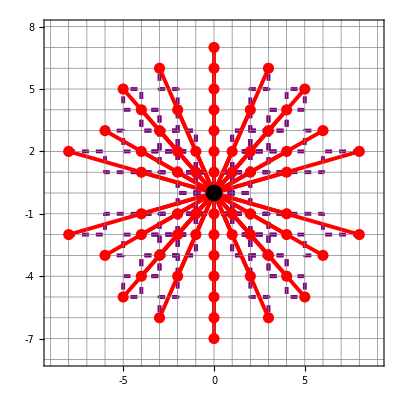

/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/bL_bT_plot_with_path.pdf

```mathematica
(*1. Define the path function*)(*Note:Wrapped in Module to keep variables local and prevent cross-contamination*)PathToLinks[sidelink_]:=Module[{ULinkslist={},linki},AppendTo[ULinkslist,{0,0,0}];
Do[linki=sidelink[[i]];
If[linki==1,AppendTo[ULinkslist,{ULinkslist[[i]][[1]]+1,ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]}]];
If[linki==-1,AppendTo[ULinkslist,{ULinkslist[[i]][[1]]-1,ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]}]];
If[linki==2,AppendTo[ULinkslist,{ULinkslist[[i]][[1]],ULinkslist[[i]][[2]]+1,ULinkslist[[i]][[3]]}]];
If[linki==-2,AppendTo[ULinkslist,{ULinkslist[[i]][[1]],ULinkslist[[i]][[2]]-1,ULinkslist[[i]][[3]]}]];
If[linki==3,AppendTo[ULinkslist,{ULinkslist[[i]][[1]],ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]+1}]];
If[linki==-3,AppendTo[ULinkslist,{ULinkslist[[i]][[1]],ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]-1}]];,{i,Length[sidelink]}];
Return[ULinkslist];]

(*2. Generate the paths and project them to 2D*)
(*We map over the 3D paths and take only the first two elements:#[[1;;2]]*)
paths3D=Table[PathToLinks[DistinctLinkPaths[[i]]],{i,Length[DistinctLinkPaths]}];
paths2D=Map[#[[1;;2]]&,paths3D,{2}];

(*3. Retrieve your top plot points*)
bLbTlist=MemDBGet[AmpDB,MemDBSelect[AmpDB,{}],{bL,bT}]//Union;

(*4. Combine everything into a single plot*)
finalPlotCombined=Graphics[{(*LAYER 1:Background paths (Purple,Dashed,Low Opacity)*){Directive[Purple,Dashed,Thickness[0.007]],Line[paths2D]},(*LAYER 2:Foreground vectors and points (Red lines/points,Black origin)*){RGBColor[1,0.0,0.0],Thickness[0.007],Line[{{0,0},#}]&/@bLbTlist},{Red,PointSize[0.02],Point[bLbTlist]},{Black,PointSize[0.03],Point[{0,0}]}},Axes->True,FrameLabel->{"",""},BaseStyle->{FontSize->18},GridLines->{Range[-10,10],Range[-10,10]},GridLinesStyle->Directive[Gray],Ticks->{Range[-10,10],Range[-10,10]},AspectRatio->1,PlotRange->{{-9,9},{-8,8}},Frame->True]

(*5. Export the final combined plot*)
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/bL_bT_plot_with_path.pdf",finalPlotCombined]
```

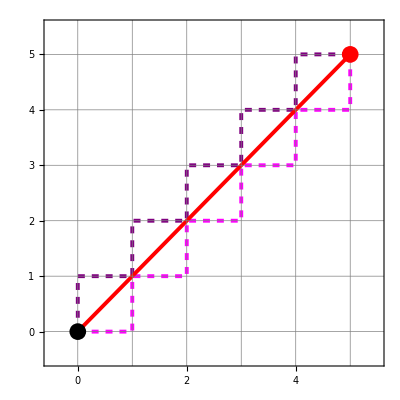

/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/Example_b_plot_with_2path.pdf

```mathematica
PathToLinks[sidelink_]:=Module[{ULinkslist={},linki},AppendTo[ULinkslist,{0,0,0}];
Do[linki=sidelink[[i]];
If[linki==1,AppendTo[ULinkslist,{ULinkslist[[i]][[1]]+1,ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]}]];
If[linki==-1,AppendTo[ULinkslist,{ULinkslist[[i]][[1]]-1,ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]}]];
If[linki==2,AppendTo[ULinkslist,{ULinkslist[[i]][[1]],ULinkslist[[i]][[2]]+1,ULinkslist[[i]][[3]]}]];
If[linki==-2,AppendTo[ULinkslist,{ULinkslist[[i]][[1]],ULinkslist[[i]][[2]]-1,ULinkslist[[i]][[3]]}]];
If[linki==3,AppendTo[ULinkslist,{ULinkslist[[i]][[1]],ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]+1}]];
If[linki==-3,AppendTo[ULinkslist,{ULinkslist[[i]][[1]],ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]-1}]];,{i,Length[sidelink]}];
Return[ULinkslist];]
seq1={2,1,2,1,2,1,2,1,2,1};
seq2={1,2,1,2,1,2,1,2,1,2};
path1Coords=PathToLinks[seq1][[All,1;;2]];
path2Coords=PathToLinks[seq2][[All,1;;2]];
distinctPathsPlot=Graphics[{(*The two stepped paths*){Thickness[0.007],Purple,Dashed,Line[path1Coords]},{Thickness[0.007],Magenta,Dashed,Line[path2Coords]},(*The direct red line from origin to {5,5}*){Thickness[0.007],Red,Line[{{0,0},{5,5}}]},(*The points:Black at origin,Red at {5,5}*){Black,PointSize[0.03],Point[{0,0}]},{Red,PointSize[0.03],Point[{5,5}]}},Axes->True,AxesOrigin->{0,0},GridLines->{Range[0,6],Range[0,6]},GridLinesStyle->Directive[Gray],Ticks->{Range[0,6],Range[0,6]},PlotRange->{{-0.5,5.5},{-0.5,5.5}},AspectRatio->1,Frame->True,FrameLabel->{"",""},BaseStyle->{FontSize->18}]
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/Example_b_plot_with_2path.pdf",distinctPathsPlot]
```

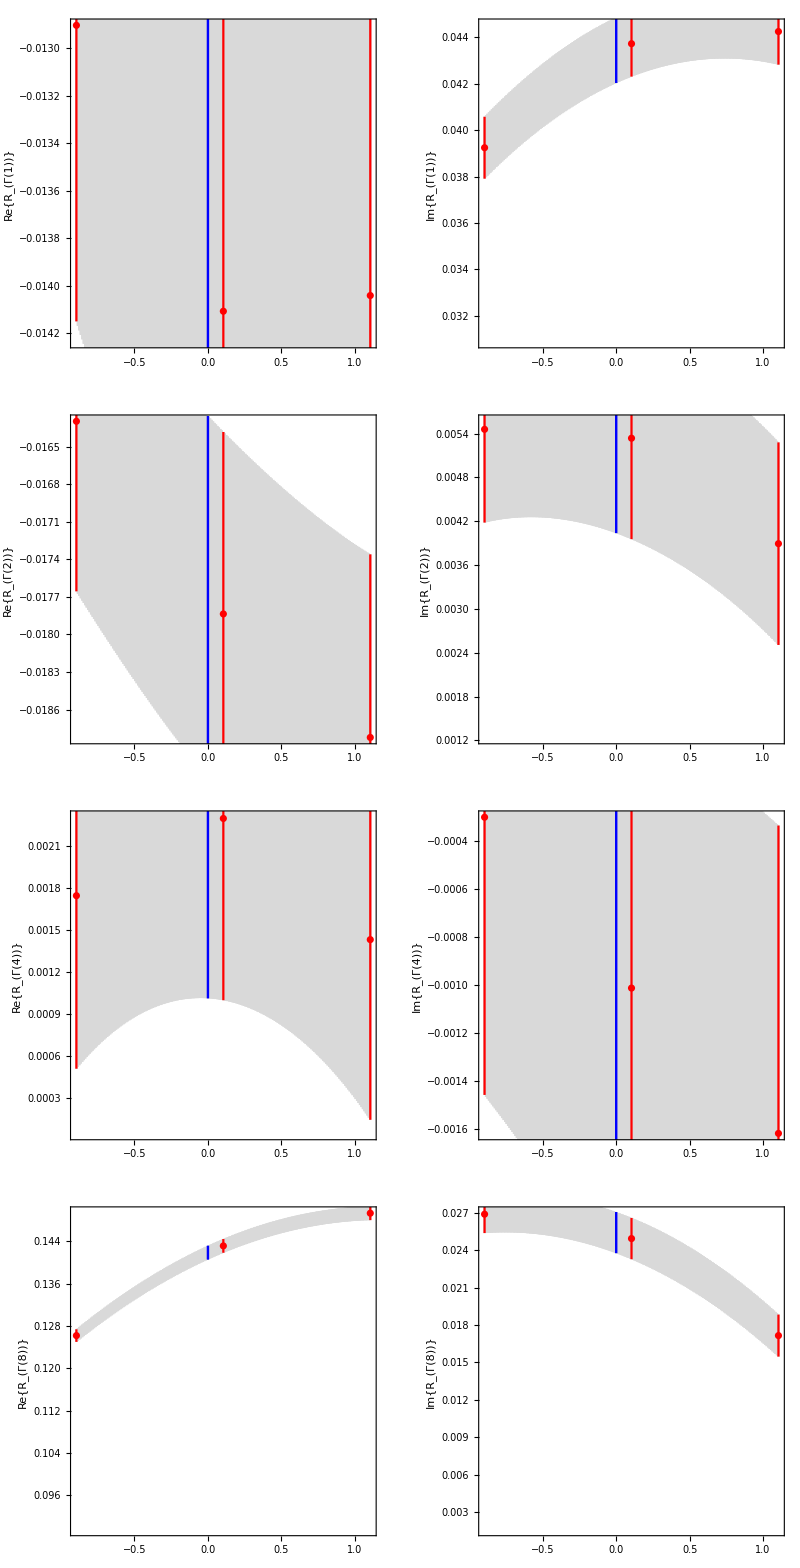

/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/Interpolation_Ex_b120_eta7_P-1.pdf

```mathematica
(*1. Define a function to generate a single plot dynamically*)makePlot[gVal_,part_]:=Module[{vvectoranddata={},v1data,blData,groupSamev,averagedTableEvengPlusImForv,dataforInterpolation={},v1dataforInterpolation={},plotforinterpolation,plotbeforinterpol,fninterpol,interpol0,yLabelStr},
Do[v1data=PathToShift[vlinksv3[[i]],3];
blData=MemDBGet[platdb,MemDBSelect[platdb,{gammaValue->gVal,linkPath->linkPatheg,sideLink->vlinksv3[[i]],numberFilter->part}],data];
AppendTo[vvectoranddata,{v1data,blData[[1]]}],{i,Length[vlinksv3]}];
groupSamev=GroupBy[vvectoranddata,First->Last];
averagedTableEvengPlusImForv=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]}]],groupSamev];
Do[AppendTo[v1dataforInterpolation,v1[averagedTableEvengPlusImForv[[i]][[1]][[3]]]-averagedTableEvengPlusImForv[[i]][[1]][[1]]];
AppendTo[dataforInterpolation,averagedTableEvengPlusImForv[[i]][[2]]];,{i,Length[averagedTableEvengPlusImForv]}];
plotforinterpolation=Transpose[{v1dataforInterpolation,dataforInterpolation}];If[Length[plotforinterpolation]<3,Return[Graphics[{Text["Not enough data for "<>ToString[gVal]<>" "<>ToString[part]]}]]];
plotbeforinterpol=ErrorListPlot[MakeErrBars[plotforinterpolation],Frame->True,PlotRangePadding->{Scaled[0.05],Scaled[0.34]},PlotStyle->Red];
fninterpol=Interpolation[plotforinterpolation,InterpolationOrder->2];
interpol0={{0,fninterpol[0]}};
yLabelStr=TraditionalForm[Row[{ToString[part],"{",Subscript["R",Row[{"Γ","(",ToString[gVal],")"}]],"}"}]];
Show[ErrorListPlot[Table[MakeErrBars[{{x,fninterpol[x]}}],{x,Min[v1dataforInterpolation],Max[v1dataforInterpolation],0.01}],PlotStyle->LightGray,Frame->True,PlotRangePadding->{Scaled[0.05],Scaled[0.38]},FrameLabel->{"",yLabelStr},BaseStyle->{FontSize->18},AspectRatio->1],ErrorListPlot[MakeErrBars[interpol0],PlotStyle->Blue,PlotRangePadding->{Scaled[0.05],Scaled[0.34]}],plotbeforinterpol]];
gammas={1,2,4,8};
parts={Re,Im};
plotGrid=Table[makePlot[g,p],{g,gammas},{p,parts}];
finalFigure=GraphicsGrid[plotGrid,ImageSize->800,Spacings->{15,15}];
finalFigure
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/Interpolation_Ex_b120_eta7_P-1.pdf",finalFigure]
```

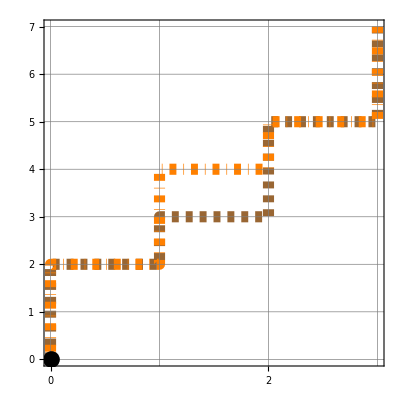

/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/Example_v_plot_with_2path.pdf

```mathematica
PathToLinks[sidelink_]:=FoldList[Plus,{0,0,0},sidelink/. {1->{1,0,0},-1->{-1,0,0},2->{0,1,0},-2->{0,-1,0},3->{0,0,1},-3->{0,0,-1}}]

seq1={3,3,1,3,1,3,3,1,3,3};
seq2={3,3,1,3,3,1,3,1,3,3};

path1Coords=PathToLinks[seq1][[All,{1,3}]];
path2Coords=PathToLinks[seq2][[All,{1,3}]];

distinctPathsPlot=Graphics[{{Thickness[0.02],Brown,Dashed,Line[path1Coords]},{Thickness[0.02],Orange,DotDashed,Line[path2Coords]},{Black,PointSize[0.03],Point[{0,0}]}},Axes->True,AxesOrigin->{0,0},GridLines->{Range[0,6],Range[0,8]},GridLinesStyle->Directive[Gray],Ticks->{Range[0,6],Range[0,8]},AspectRatio->1,Frame->True,FrameLabel->{"",""},BaseStyle->{FontSize->18}]
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/plots_for_Thesis/Example_v_plot_with_2path.pdf",distinctPathsPlot]
```